```mathematica
SetDirectory[NotebookDirectory[]];
raw = OpenRead["reviews.csv"];
reviews = Map[StringSplit[#, "|"]&, ReadList[raw, String]];
(*start pre-processing data*)
(*spell checking, tokenization, remove symbols*)
(*extract words from dataset*)
numOfReviews=Length[reviews];
indexOfReviews=2;
$RecursionLimit=Infinity;
reviewsWords = List[];
While[indexOfReviews≤ 50000,
review=reviews[[indexOfReviews]];
reviewStr=review[[2]];
newReviewStr = DeleteStopwords[reviewStr];
reviewWords=TextWords[newReviewStr];
reviewWords = WordStem[reviewWords];
reviewWords = ToLowerCase[reviewWords];
reviewWords = DeleteDuplicates[reviewWords];
numOfWords = Length[reviewWords];
indexOfWord = 1;
indexesOfDeleteWord = List[];
correctedReviewWords = List[];
While[indexOfWord ≤ numOfWords,
If[DictionaryWordQ[reviewWords[[indexOfWord]]] == True,correctedReviewWords = Append[correctedReviewWords, reviewWords[[indexOfWord]]];
];
indexOfWord++;
];

reviewsWords = Append[reviewsWords, correctedReviewWords];
indexOfReviews++;
];
Export["pre-processingWords_50k.mx", reviewsWords];
(*feature extractor TF-IDF*)

(*Dimension Reduce*)

(*create training dataset*)
(*create testing dataset*)
(*train SVM*)
(*test*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
raw = OpenRead["reviews.csv"];
reviews = Map[StringSplit[#, "|"]&, ReadList[raw, String]];
$RecursionLimit=$IterationLimit = Infinity;
reviewsWords = Import["pre-processingWords_50k.mx"]
fe=FeatureExtraction[reviewsWords,"TFIDF"]
features=fe[reviewsWords];
listOfFeatures=List@@features;
listOfFeatures = DimensionReduce[listOfFeatures, 100];
testData=Take[listOfFeatures,{1,-1,5}];
trainData=Drop[listOfFeatures,{1,-1,5}];
indexOfReviews=2;
classes=List[];
While[indexOfReviews≤50000,
review=reviews[[indexOfReviews]];
class=Take[review,1];
classes=Append[classes,class[[1]]];
indexOfReviews++;
];
testClasses=Take[classes,{1,-1,5}];
trainClasses=Drop[classes,{1,-1,5}];
trainingSet=trainData->trainClasses;
testingSet = testData -> testClasses;
```

{{great,love,pat,listen,year,good,mood,make,feel,better,bad,just,like,sugar,rain,life,vocal,lyric,kill,hidden,gem,desert,isl,book,big,beyond,matter,black,white,young,old,male,thing,sing},49997,{diva,maintain,music,entertain,goddess,proven,3,21st,sound,great,timeless,year,come}}
 |  |  |  |

FeatureExtractorFunction[…]

```mathematica
$RecursionLimit=$IterationLimit = Infinity;
svm=Classify[trainingSet,Method->"SupportVectorMachine"];
(*rf = Classify[trainingSet, Method->"RandomForest"];
nn = Classify[trainingSet, Method->"NeuralNetwork"];*)
svmCM = ClassifierMeasurements[svm, testingSet];(*rfCM = ClassifierMeasurements[rf, testingSet]；
nnCM = ClassifierMeasurements[nn, testingSet];*)
svmCM["Accuracy"]
svmCM["Precision"]
svmCM["Recall"]
svmCM["ROCCurve"]
(*rfCM["Accuracy"]
rfCM["Precision"]
rfCM["Recall"]
rfCM["ROCCurve"]
nnCM["Accuracy"]
nnCM["Precision"]
nnCM["Recall"]
nnCM["ROCCurve"]*)
```

0.8101

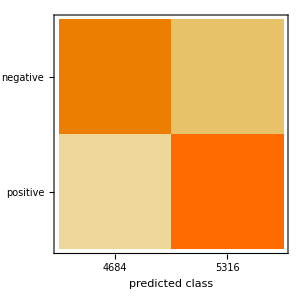
```mathematica
-Graphics-<|"negative"->0.8204526046114432,"positive"->0.8009781790820165|>
```

<|negative→0.784126,positive→0.835066|>

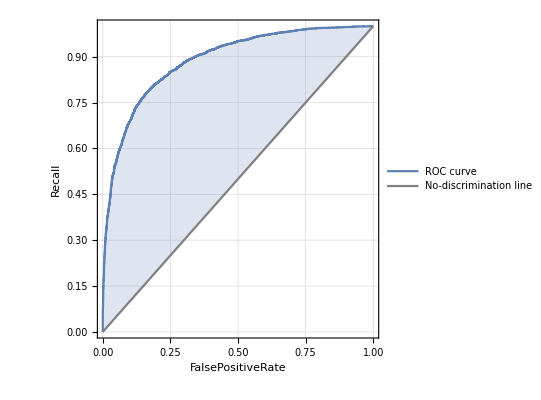
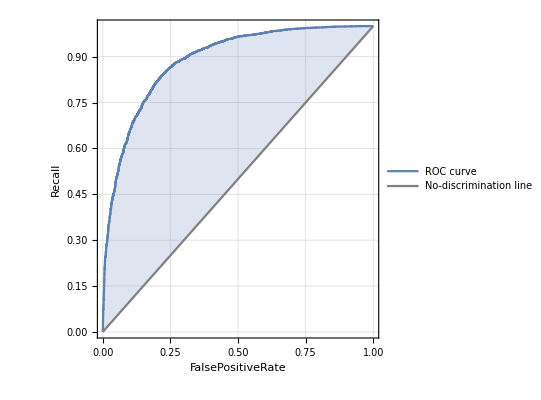
<|negative→-Graphics-,positive→-Graphics-|>